```mathematica
Manipulate[ParametricPlot3D[{-10*Cos[α]/Log[t],-10*Sin[α]/Log[t],-t},{t,1,n},{α,0,π/180*j},PlotRange->{{-15,15},{-15,15},{-15,-1}},Axes->False,Boxed->False,ImageSize->Large,ColorFunction->Hue,SphericalRegion->True],{{j,360,"revolution"},1,360,Appearance-> "Labeled"},{{n,10,"maximum x"},1.0001,30,Appearance-> "Labeled"}]
```

```mathematica
pres[h_]:=101325 (1-0.0000226 h)^5.259
temp[h_]:=288.15-0.0065 h
avden[h_]:=0.00348 pres[h/2]/temp[h/2]
f[e_,d_]:=1/(4 Log[10,(1.25 e)/(3.7 d)]^2)
v[h_,d_]:=Sqrt[(2 (101325-pres[h]) d)/(f[1.4 d+150,d] h avden[h])]
y[h_,d_,t_,i_]:=(h/1000)(1+Cos[Pi t/p[h,d,i]])
r[h_,d_,t_,i_]:=If[t<p[h,d,i],i (d/1000) Csc[Pi y[h,d,t,i] 500/h],1.7+d/260-Abs[((t-p[h,d,i]-15)/10)]^3]
p[h_,d_,i_]:=(3 h)/((3-i) v[h,d])
```

```mathematica
Manipulate[
Show[Graphics3D[{
(*Ground*)
(* Style[Cuboid[{-8,-8,-0.1},{8,8,0.25}],RGBColor[0.1,0.5,0.1,.4]],*)
(*Cloud*)
(*Style[Cuboid[{-8,-8,2.5},{8,8,h/500}],GrayLevel[0.4],Opacity[0.2],EdgeForm[]],*)
(*Red Arrow*)
(*Style[Arrow[{{0,0,h/600},{0,0,h/600-v[h,d]/20}}],RGBColor[1,0,0],Thickness[0.005]],*)
(*BSpline Curves*)
(*Style[Table[Rotate[Arrow[BSplineCurve[{{d/150,0,h/520},{d/500,0,h/520},{d/820,0,h/1000},{d/500,0,1},{1.5+d/300,0,0.5},{2+d/260,0,1.25},{1.5+d/350,0,2.3},{1.5+d/450,0,1.25}}]],q,{0,0,1}],{q,0,7 Pi/4,Pi/4}],Opacity[0.6+v[h,d]/200],Arrowheads[0.025]],*)
(*Rings*)
Style[Table[If[t<(1.4-d/10000) p[h,d,i],Translate[Line[Table[{r[h,d,t,i] Cos[q],r[h,d,t,i] Sin[q],0},{q,0,2 Pi,Pi/32}]],{0,0,y[h,d,t,i]}]],{i,0.2,1,0.2}],GrayLevel[0.8],Thickness[0.005]]},
ImageSize->{550,360},Boxed->False,RotationAction->"Clip",ViewAngle->Pi/14,PlotRange->{{-8,8},{-8,8},{-0.1,h/500+0.1}}],
(*Plots*)
ParametricPlot3D[{(d/1000) Csc[Pi z 500/h] Cos[q],(d/1000) Csc[Pi z 500/h] Sin[q],z},{q,0,2 Pi},{z,0.1,h/500-0.1},
PlotStyle->Directive[GrayLevel[0.3],Opacity[.5]],Mesh-> True],Alignment-> Center],
{{d,700,"diameter (m)"},500,1000,Appearance->"Labeled"},{{h,3000,"height (m)"},2500,5000,Appearance->"Labeled"},{{t,0,"time (s)"},0,90,Appearance->"Labeled"},SaveDefinitions->True]
```

```mathematica
Panel[DynamicModule[{y=.5},EventHandler[Column[{Plot3D[Exp[-x^2-y^2],{x,-4,4},{y,-4,4},PlotRange->1,ViewAngle->Dynamic@y,ImageSize->400]}],"MouseDown":>init=y+Last@MousePosition["Graphics"],"MouseDragged":>y=Clip[init-Last@MousePosition["Graphics"],{.2,1}]]]]
```

Last::normal: Nonatomic expression expected at position 1 in Last[None].

Set::write: Tag RuleDelayed in "MouseDown" :> init is Protected.

Set::write: Tag RuleDelayed in "MouseDragged" :> y$141440 is Protected.

```mathematica
DynamicModule[{pt={0,0}},Panel[ClickPane[Framed@Graphics[{Yellow,Dynamic@Disk[pt]},PlotRange->5],(pt=#)&]]]
```

```mathematica
DynamicModule[{pos={0,0}},Graphics[{GestureHandler[Disk[Dynamic[pos]],"Drag":>(pos+=#&)]},PlotRange->{{-5,5},{-5,5}}]]
```

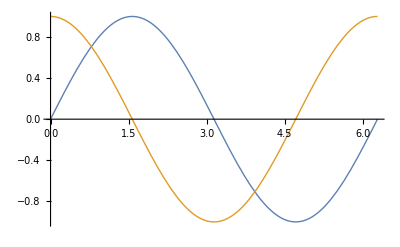

```mathematica
Plot[{Annotation[Sin[x],"Sine","Mouse"],Annotation[Cos[x],"Cosine","Mouse"]},{x,0,2 π},PlotStyle->Thick]
```

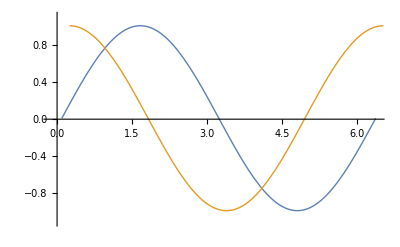

-Graphics-

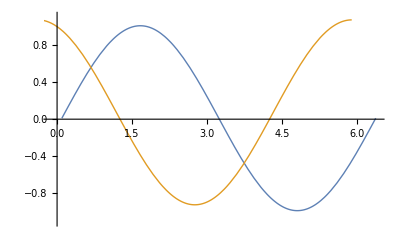

-Graphics-

```mathematica
ParametricPlot3D[{Annotation[{1*Cos[x],1*Sin[x],0},"Circle1","MouseDragged"],Annotation[{2*Cos[x],2*Sin[x],0},"Circle2","MouseDragged"]},{x,0,2π},Axes->True,PlotRange-> All ,Boxed->True]
```

-Graphics3D-

```mathematica
g[1]=ExampleData[{"TestImage","Girl"}];
g[2]=ExampleData[{"TestImage","Girl2"}];
g[3]=ExampleData[{"TestImage","Girl3"}];
Manipulate[Plot[Cos[x^n],{x,0,4Pi},Epilog->Table[Inset[g[i],pos[[i]],{0,0},ImageScaled[{.2,.2}]],{i,3}]],{{n,1},0,4},{{pos,{{0,0},{Pi,0},{2Pi,0}}},Locator,Appearance->None}]
```